## defining model

```mathematica
changepoint=0.451985;
```

```mathematica
λ[t_]:=Piecewise[{{1,t<changepoint},{2,t≥changepoint}}]
```

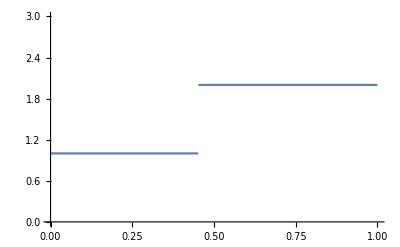

```mathematica
Plot[λ[t],{t,0,1},PlotRange->{0,3}]
```

```mathematica
ts={0,0.095310,0.200671,0.318454,changepoint,0.606136,0.788457,1.011601,1.299283,1.704748,2.397895,Infinity};
```

```mathematica
n=Length[ts]-2;
```

```mathematica
t[i_]:=ts[[i+1]];
```

```mathematica
Omega[t1_,t2_]:=Integrate[1/λ[s],{s,t1,t2}]
```

```mathematica
io[i_]:=Omega[t[i],t[i+1]]
```

```mathematica
(*Pi*)
```

## calculating probabilities and expectations

```mathematica
pi[i_,j_]:=Piecewise[{
{3/2*Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])(1-Exp[-Omega[t[j],t[j+1]]]),0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/2 Exp[-3Omega[0,t[i]]](2-3Exp[-(t[i+1]-t[i])/λ[t[i]]]+Exp[-3(t[i+1]-t[i])/λ[t[i]]]),
0≤i==j≤n&&(i∈Integers&&j∈Integers)}}]
```

```mathematica
(*Pi is working, at least for constant N [λ]*)
```

```mathematica
(*E[t_3]*)
```

```mathematica
intEt3[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t3 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et3[i_,j_]:=Piecewise[{
{3/(4pi[i,j])Exp[-3Omega[0,t[i]]](1-Exp[-Omega[t[j],t[j+1]]])Exp[-Omega[t[i+1],t[j]]]((λ[t[i]]+2t[i])Exp[-Omega[t[i],t[i+1]]]-
(λ[t[i]]+2t[i+1])Exp[-3Omega[t[i],t[i+1]]]),
0<=i<j≤n&&(i∈Integers&&j∈Integers)},
{1/(12pi[i,i])Exp[-3Omega[0,t[i]]](4(3t[i]+λ[t[i]])+
Exp[-3Omega[t[i],t[i+1]]](6t[i+1]+5λ[t[i]])-9Exp[-Omega[t[i],t[i+1]]](2t[i]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[i]+λ[t[i]]/3.0,i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

```mathematica
(*Et2*)
intEt2[i_,j_]:=1/pi[i,j] Integrate[3/(λ[t[i]]λ[t[j]]) t2 Exp[-3Omega[0,t3]]Exp[-Omega[t3,t2]],{t2,t[j],t[j+1]},{t3,t[i],t[i+1]}]
```

```mathematica
Et2[i_,j_]:=Piecewise[{
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]-(λ[t[j]]+t[j+1])Exp[-Omega[t[j],t[j+1]]]),
0≤i<j<n&&(i∈Integers&&j∈Integers)},
{3/(2pi[i,j])Exp[-3Omega[0,t[i]]]Exp[-Omega[t[i+1],t[j]]](Exp[-Omega[t[i],t[i+1]]]-Exp[-3Omega[t[i],t[i+1]]])*
(λ[t[j]]+t[j]),
0≤i<j==n&&(i∈Integers&&j∈Integers)},
{1/(6pi[i,j])Exp[-3Omega[0,t[i]]](Exp[-3Omega[t[i],t[i+1]]](3t[i+1]+λ[t[i]])+6t[i]+8λ[t[i]]-9Exp[-Omega[t[i],t[i+1]]](t[i+1]+λ[t[i]])),
0≤i==j<n&&(i∈Integers&&j∈Integers)},
{t[n]+λ[t[n]]/3+λ[t[n]],
i==j==n&&(i∈Integers&&j∈Integers)}
}]
```

## calculating transitions

```mathematica
intqts[i_,j_,k_,l_]:=Piecewise[{
{(*case A*)
Assuming[{s3,s2,t2,t3,u}∈Reals,Integrate[(1/(2s2+s3)Exp[-3Omega[u,s3]]Exp[-2Omega[s3,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,0,Et3[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]+Integrate[(2/(2s2+s3)Exp[-2Omega[u,s2]]*1/λ[t2] Exp[-Omega[s2,t2]])*DiracDelta[t3-Et3[i,j]]/.{s3->Et3[i,j],s2->Et2[i,j]},{u,Et3[i,j],Et2[i,j]},{t2,t[l],t[l+1]},{t3,t[k],t[k+1]}]]
,
0≤i==k<j<l&&{i,j,k,l}∈Integers
},
{(*case B*)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]]*1/λ[t2]),{u,0,Et3[i,j]},{t2,t[l],t[l+1]}]+
NIntegrate[(2/(2Et2[i,j]+Et3[i,j])1/λ[t2] Exp[-2Omega[u,t2]]),{t2,t[l],t[l+1]},{u,Et3[i,j],t2}]],
0≤i==k<l<j&&{i,j,k,l}∈Integers
},
{ (* case C *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(1/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==l<j&&{i,j,k,l}∈Integers
},
{ (* case D *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,t3]]),{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i<j==l&&{i,j,k,l}∈Integers
},
{ (* case E *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*2/λ[t3]*Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]]),{t3,t[k],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]Exp[-Omega[Et2[i,j],t2]]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t2]],{t2,Et3[i,j],t[l+1]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-2Omega[u,t2]],{t2,Et3[i,j],t[l+1]},{u,Et3[i,j],t2}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[1/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],Et3[i,j]},{u,0,t3}]],
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],t3]],{t3,t[k],Et2[i,j]},{u,0,Et3[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t2] Exp[-3Omega[u,Et3[i,j]]]Exp[-2Omega[Et3[i,j],Et2[i,j]]]*Exp[-Omega[Et2[i,j],t2]],{t2,Et2[i,j],t[k+1]},{u,0,Et3[i,j]}]],
0≤i<k==l==j≤n&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]]+Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-2 Omega[u,Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,Et3[i,j],Et2[i,j]}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[(2 Exp[-3 Omega[u,Et3[i,j]]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t2]])/((2 Et2[i,j]+Et3[i,j]) λ[t2]),{t2,t[l],t[l+1]},{u,0,Et3[i,j]}]],
0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*2/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]]+
Assuming[{s3,s2,t2,t3,u}∈Reals,NIntegrate[2/(2Et2[i,j]+Et3[i,j])*1/λ[t3] Exp[-3Omega[u,t3]],{t3,t[k],t[k+1]},{u,0,t3}]],
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

```mathematica
qts[i_,j_,k_,l_]:=Piecewise[{
{(* case A *)
1/(2Et2[i,j]+Et3[i,j])1/λ[t[l]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Exp[-2Omega[t[i+1],Et2[i,j]]](1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2+
Sum[Exp[-2Omega[t[a+1],Et2[i,j]]](1-Exp[-2io[a]])*λ[t[a]]/2,{a,i+1,j-1}]+(1-Exp[-2(Et2[i,j]-t[j])/λ[t[j]]])*λ[t[j]]/2)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0<=i==k<j<l≤n&&{i,j,k,l}∈Integers
},
{ (* case B *)
1/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
Exp[-2(*notice the 2*)Omega[Et3[i,j],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*(1-Exp[-2(t[i+1]-Et3[i,j])/λ[t[i]]])*λ[t[i]]/2*Exp[-2Omega[t[i+1],t[l]]]*λ[t[l]]/2(1-Exp[-2io[l]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]](λ[t[l]]/2(1-Exp[-2io[l]])Sum[(1-Exp[-2io[a]])*λ[t[a]]/2 Exp[-2Omega[t[a+1],t[l]]],{a,i+1,l-1}])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[l]]*λ[t[l]]/2(t[l+1]-t[l]-λ[t[l]]/2(1-Exp[-2io[l]])),
0<=i==k<l<j≤n&&{i,j,k,l}∈Integers
},
{(* case C *)
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case D *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(λ[t[k]]/3(1-Exp[-3io[k]])Sum[(1-Exp[-3io[a]])*λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]+λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i<j==l≤n&&{i,j,k,l}∈Integers
},
{(* case E *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*Exp[-2Omega[Et3[i,j],t[k]]]*λ[t[k]]/2(1-Exp[-2io[k]]),
0≤i<k<j==l&&{i,j,k,l}∈Integers
},
{ (* case F *)
2/(2Et2[i,j]+Et3[i,j])Exp[-2Omega[Et3[i,j],Et2[i,j]]]*1/λ[t[l]]*
(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)Exp[-Omega[Et2[i,j],t[l]]]λ[t[l]](1-Exp[-io[l]]),
0≤i<j==k<l&&{i,j,k,l}∈Integers
},
{ (* case G and G2 *)
1/(2Et2[i,j]+Et3[i,j])*(1/λ[t[k]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]]/2*
(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]])+t[k+1]-Et3[i,j]-λ[t[k]]/2(1-Exp[-2(t[k+1]-Et3[i,j])/λ[t[k]]]))+
1/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](Sum[(1-Exp[-3io[a]])*λ[t[a]]/3*Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}]*λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]])+λ[t[k]]/3(Et3[i,j]-t[k]-λ[t[k]]/3(1-Exp[-3(Et3[i,j]-t[k])/λ[t[k]]]))),
0≤i==k==l<j≤n&&{i,j,k,l}∈Integers
},
{ (* case H and H2 *)
1/(2Et2[i,j]+Et3[i,j])*4/λ[t[k]]*Exp[-2Omega[Et3[i,j],t[k]]](Sum[Exp[-3Omega[t[a+1],Et3[i,j]]]*(1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*
λ[t[k]]/2(1-Exp[-2(Et2[i,j]-t[k])/λ[t[k]]])+
2/(2Et2[i,j]+Et3[i,j])*1/λ[t[k]] Exp[-2Omega[Et3[i,j],Et2[i,j]]]*(Sum[Exp[-3Omega[t[a+1],Et3[i,j]]](1-Exp[-3io[a]])*λ[t[a]]/3,{a,0,i-1}]+
(1-Exp[-3(Et3[i,j]-t[i])/λ[t[i]]])*λ[t[i]]/3)*λ[t[k]](1-Exp[-(t[k+1]-Et2[i,j])/λ[t[k]]]),
0≤i<k==l==j&&{i,j,k,l}∈Integers
},
{ (* case I and I2 *)
1/(2 Et2[i,j]+Et3[i,j])(1/λ[t[l]] Exp[-2 Omega[Et3[i,j],Et2[i,j]]] (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]])+1/(λ[t[l]] 2)2 λ[t[i]] (1-Exp[-(2 (Et2[i,j]-Et3[i,j]))/λ[t[i]]]) Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]))+
1/((2 Et2[i,j]+Et3[i,j]) λ[t[l]])2 Exp[-2 Omega[Et3[i,j],Et2[i,j]]] Exp[-Omega[Et2[i,j],t[l]]] λ[t[l]] (1-Exp[-io[l]]) (∑_(a=0)^(i-1) 1/3 Exp[-3 Omega[t[a+1],Et3[i,j]]] (1-Exp[-3 io[a]]) λ[t[a]]+1/3 (1-Exp[-(3 (Et3[i,j]-t[i]))/λ[t[i]]]) λ[t[i]]),

0≤i==j==k<l&&{i,j,k,l}∈Integers
},
{ (* case J and J2 *)
2/(2Et2[i,j]+Et3[i,j])*2/λ[t[k]](λ[t[k]]/3(1-Exp[-3io[k]])(Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}])+λ[t[k]]/3*
(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]])))+
2/(2Et2[i,j]+Et3[i,j])1/λ[t[k]](Sum[(1-Exp[-3io[a]])λ[t[a]]/3 Exp[-3Omega[t[a+1],t[k]]],{a,0,k-1}] λ[t[k]]/3(1-Exp[-3io[k]])+
λ[t[k]]/3(t[k+1]-t[k]-λ[t[k]]/3(1-Exp[-3io[k]]))),
0≤k<i==j==l&&{i,j,k,l}∈Integers
}
}]
```

## exporting

```mathematica
numStates = (n+1)(n+2)/2
```

66

```mathematica
getIndex[i_,j_,n_]:=i*n-i(i-1)/2+j+1;
```

```mathematica
allqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allqts[[ijIdx,klIdx]]=qts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_qtsprobs.csv",allqts]
```

mathematica_qtsprobs.csv

```mathematica
allintqts = Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
For[i=0,i≤n,i++,
Print[i];
For[j=i,j≤n,j++,
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
ijIdx = getIndex[i,j,n];
klIdx=getIndex[k,l,n];
allintqts[[ijIdx,klIdx]]=intqts[i,j,k,l];
]
]
]
]
```

0

1

2

3

4

5

6

7

8

9

10

```mathematica
Export["mathematica_intqtsprobs.csv",allintqts]
```

mathematica_intqtsprobs.csv

```mathematica
pts[i_,j_,k_,l_,ρ_]:=
```

## making pts transitions

```mathematica
pts[i_,j_,k_,l_,ρ_]:=Module[{treeSize, probRecomb},treeSize=3*Et3[i,j]+2*(Et2[i,j]-Et3[i,j]); probRecomb=1-Exp[-treeSize*ρ/2];qts[i,j,k,l]*probRecomb]
```

```mathematica
pts[4,4,2,4,0.0001]
```

6.34354×10^-6

## emission probabilities

```mathematica
emit[k_,i_,j_,Td_,θ_]:=Piecewise[{
{
Exp[(-θ(2Et2[i,j]+Et3[i,j]+3Td))/2],
k==0
},
{
Exp[-θ/2*(Et2[i,j]-Et3[i,j])](1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==1
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)],
k==2
},
{
(1-Exp[-θ/2(Et2[i,j]-Et3[i,j])])(1-Exp[-θ/2(2Et3[i,j]+Et2[i,j]+3Td)]),
k==3
}
}]
```

### Emissions output

```mathematica
numStates = (n+1)(n+2)/2;
```

```mathematica
ρ=0.001;θ=0.001;Td=0.2;
```

```mathematica
emissionsout =Table[0,{i,1,numStates},{j,1,6}];
```

```mathematica
getIndex[i_,j_,n_]:=i*n-i(i-1)/2+j+1;
```

```mathematica
Module[{state,i,j,k},
For[i=0,i≤n,i++,
For[j = i, j≤n,j++,
state=getIndex[i,j,n];
emissionsout[[state,1]] = i;
emissionsout[[state,2]] = j;
For[k=0,k≤3,k++,
emissionsout[[state,k+3]] = emit[k,i,j,Td,θ];
Print[emissionsout[[state,k+3]]]
]
]
]
]
```

```mathematica
emissionsout//TableForm
```

0 | 0 | 0.999622 | 0.000361719 | 0.0000159948 | 5.78781×10^-9
0 | 1 | 0.99953 | 0.000419565 | 0.0000504394 | 2.11726×10^-8
0 | 2 | 0.999419 | 0.000475182 | 0.000106076 | 5.04349×10^-8
0 | 3 | 0.999293 | 0.000537773 | 0.000168691 | 9.07817×10^-8
0 | 4 | 0.999149 | 0.000609844 | 0.000240788 | 1.46968×10^-7
0 | 5 | 0.998982 | 0.000693632 | 0.000324607 | 2.25387×10^-7
0 | 6 | 0.99878 | 0.000794465 | 0.000425477 | 3.3844×10^-7
0 | 7 | 0.998526 | 0.000921205 | 0.000552264 | 5.09499×10^-7
0 | 8 | 0.998183 | 0.00109234 | 0.00072346 | 7.91701×10^-7
0 | 9 | 0.997648 | 0.00135954 | 0.000990758 | 1.35015×10^-6
0 | 10 | 0.99529 | 0.00253633 | 0.00216799 | 5.52475×10^-6
1 | 1 | 0.999471 | 0.00051093 | 0.000017691 | 9.04365×10^-9
1 | 2 | 0.999369 | 0.000575147 | 0.0000560986 | 3.22854×10^-8
1 | 3 | 0.999243 | 0.000637729 | 0.000118713 | 7.57643×10^-8
1 | 4 | 0.999099 | 0.000709789 | 0.000190811 | 1.35557×10^-7
1 | 5 | 0.998932 | 0.000793564 | 0.000274629 | 2.18169×10^-7
1 | 6 | 0.99873 | 0.000894382 | 0.0003755 | 3.36267×10^-7
1 | 7 | 0.998476 | 0.0010211 | 0.000502286 | 5.13669×10^-7
1 | 8 | 0.998134 | 0.00119221 | 0.000673482 | 8.04434×10^-7
1 | 9 | 0.997598 | 0.00145937 | 0.00094078 | 1.37625×10^-6
1 | 10 | 0.99524 | 0.00263598 | 0.00211801 | 5.60974×10^-6
2 | 2 | 0.999304 | 0.00067662 | 0.0000197898 | 1.33995×10^-8
2 | 3 | 0.999188 | 0.000748792 | 0.0000631914 | 4.73557×10^-8
2 | 4 | 0.999044 | 0.000820839 | 0.000135289 | 1.11157×10^-7
2 | 5 | 0.998876 | 0.0009046 | 0.000219107 | 1.98427×10^-7
2 | 6 | 0.998674 | 0.0010054 | 0.000319978 | 3.22133×10^-7
2 | 7 | 0.998421 | 0.0011321 | 0.000446765 | 5.06583×10^-7
2 | 8 | 0.998078 | 0.00130318 | 0.00061796 | 8.06864×10^-7
2 | 9 | 0.997543 | 0.00157029 | 0.000885258 | 1.39354×10^-6
2 | 10 | 0.995185 | 0.00274671 | 0.00206249 | 5.69247×10^-6
3 | 3 | 0.999115 | 0.000862889 | 0.0000224544 | 1.93928×10^-8
3 | 4 | 0.998981 | 0.00094577 | 0.000072838 | 6.89582×10^-8
3 | 5 | 0.998814 | 0.00102952 | 0.000156656 | 1.61472×10^-7
3 | 6 | 0.998612 | 0.0011303 | 0.000257527 | 2.91487×10^-7
3 | 7 | 0.998358 | 0.00125697 | 0.000384314 | 4.83867×10^-7
3 | 8 | 0.998016 | 0.00142802 | 0.00055551 | 7.94856×10^-7
3 | 9 | 0.997481 | 0.00169508 | 0.000822808 | 1.39825×10^-6
3 | 10 | 0.995123 | 0.00287128 | 0.00200004 | 5.77081×10^-6
4 | 4 | 0.998896 | 0.00107784 | 0.0000258176 | 2.78581×10^-8
4 | 5 | 0.998741 | 0.00117425 | 0.0000843126 | 9.91286×10^-8
4 | 6 | 0.99854 | 0.00127501 | 0.000185183 | 2.36455×10^-7
4 | 7 | 0.998286 | 0.00140166 | 0.00031197 | 4.38026×10^-7
4 | 8 | 0.997943 | 0.00157267 | 0.000483166 | 7.61424×10^-7
4 | 9 | 0.997408 | 0.00183967 | 0.000750464 | 1.38419×10^-6
4 | 10 | 0.995051 | 0.00301561 | 0.00192769 | 5.84209×10^-6
5 | 5 | 0.998643 | 0.00132663 | 0.0000305583 | 4.05946×10^-8
5 | 6 | 0.998456 | 0.00144232 | 0.000101561 | 1.4671×10^-7
5 | 7 | 0.998202 | 0.00156893 | 0.000228348 | 3.58909×10^-7
5 | 8 | 0.99786 | 0.0017399 | 0.000399544 | 6.96658×10^-7
5 | 9 | 0.997325 | 0.00200684 | 0.000666842 | 1.34183×10^-6
5 | 10 | 0.994968 | 0.00318248 | 0.00184407 | 5.89841×10^-6
6 | 6 | 0.998337 | 0.00162528 | 0.0000374412 | 6.09537×10^-8
6 | 7 | 0.998102 | 0.00177008 | 0.000127821 | 2.26684×10^-7
6 | 8 | 0.997759 | 0.001941 | 0.000299017 | 5.81695×10^-7
6 | 9 | 0.997225 | 0.00220786 | 0.000566315 | 1.25382×10^-6
6 | 10 | 0.994867 | 0.00338315 | 0.00174354 | 5.9291×10^-6
7 | 7 | 0.997952 | 0.00199916 | 0.0000483517 | 9.68612×10^-8
7 | 8 | 0.997633 | 0.00219335 | 0.000172913 | 3.80157×10^-7
7 | 9 | 0.997099 | 0.00246011 | 0.00044021 | 1.08612×10^-6
7 | 10 | 0.994742 | 0.00363495 | 0.00161744 | 5.91039×10^-6
8 | 8 | 0.997431 | 0.00250028 | 0.0000683438 | 1.71319×10^-7
8 | 9 | 0.996929 | 0.00279934 | 0.000270698 | 7.60109×10^-7
8 | 10 | 0.994573 | 0.00397358 | 0.00144793 | 5.78485×10^-6
9 | 9 | 0.996614 | 0.0032685 | 0.000117462 | 3.85228×10^-7
9 | 10 | 0.994313 | 0.00449502 | 0.00118707 | 5.36643×10^-6
10 | 10 | 0.993127 | 0.00587361 | 0.000993624 | 5.87655×10^-6

```mathematica
Export["/home/peter/bio/snail/tsmc/emissions_mma_output.csv",emissionsout];
```

## α’s and β’s check (forward and backward)

```mathematica
data = {0,0,1,0};
```

```mathematica
alpha = Table[0,{i,1,4},{j,1,numStates}];
```

```mathematica
beta = Table[0,{i,1,4},{j,1,numStates}];
```

```mathematica
normconst=Table[0,{i,1,4}];
```

```mathematica
(* first alphas *)
```

```mathematica
getIndex[65,65,n]
```

-1364

```mathematica
Module[{i,j,k,ijidx},
For[i=0,i<=n,i++,
For[j=i,j<=n,j++,
ijidx=getIndex[i,j,n];
alpha[[1,ijidx]] = pi[i,j]*emit[data[[1]],i,j,Td,θ];
]
];
normconst[[1]]=Total[alpha[[1,All]]];
alpha[[1,All]]=alpha[[1,All]]/normconst[[1]];
]
```

```mathematica
?Print
```

Print[expr] prints expr as output.

```mathematica
Module[{i,j,ijidx,t,sum},
For[t=1,t≤3,t++,
Print["t=",t];
sum=0.0;
For[i=0,i≤n,i++,
Print["i=",i];
For[j=i,j≤n,j++,
Print["j=",j];
ijidx = getIndex[i,j,n];
alpha[[t+1,ijidx]]=Total[Table[pts[k,l,i,j,ρ],{k,0,n},{l,i,n}]]*emit[data[[t+1]],i,j,Td,θ];
]
];
normconst[[t+1]]=Total[alpha[[t+1]]];
alpha[[t+1,All]]=alpha[[t+1,All]]/normconst[[t+1]];
]
]
```

t=1

i=0

j=0

j=1

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=1

j=1

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=2

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=3

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=4

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=5

j=5

j=6

j=7

j=8

j=9

j=10

i=6

j=6

j=7

j=8

j=9

j=10

i=7

j=7

j=8

j=9

$Aborted

```mathematica
alpha
```

{{0.0120165,0.0236554,0.0236526,0.0236496,0.0122786,0.0133498,0.0147635,0.016753,0.0198653,0.0258751,0.0623204,0.0108884,0.021399,0.0213963,0.0111087,0.0120779,0.0133568,0.0151568,0.0179726,0.0234098,0.0563827,0.00976028,0.0191429,0.00993874,0.0108059,0.0119501,0.0135605,0.0160798,0.0209443,0.0504446,0.00863242,0.00876891,0.00953398,0.0105436,0.0119644,0.0141871,0.0184791,0.0445071,0.00207218,0.00444889,0.00491999,0.00558301,0.00662021,0.008623,0.0207686,0.00225798,0.00491956,0.00558252,0.00661962,0.00862224,0.0207667,0.00250519,0.00558198,0.00661899,0.00862141,0.0207647,0.00285735,0.00661814,0.0086203,0.0207621,0.0034198,0.00861884,0.0207585,0.00455444,0.0207531,0.0138189},{{0.,3.1946×10^-6,3.19442×10^-6,3.19422×10^-6,3.19399×10^-6,3.19372×10^-6,3.1934×10^-6,3.193×10^-6,3.19245×10^-6,3.19159×10^-6,3.18782×10^-6},{6.9683×10^-6,0.0000124078,0.0000156128,0.0000156118,0.0000156107,0.0000156094,0.0000156078,0.0000156058,0.0000156032,0.000015599,0.0000155805},{6.96749×10^-6,0.0000114711,0.0000206759,0.0000261494,0.0000261475,0.0000261453,0.0000261426,0.0000261393,0.0000261348,0.0000261278,0.000026097},{6.9666×10^-6,0.0000114696,0.0000220003,0.0000289404,0.0000383426,0.0000383394,0.0000383355,0.0000383306,0.0000383241,0.0000383138,0.0000382685},{3.61697×10^-6,5.95487×10^-6,0.0000114223,0.0000177488,0.0000372004,0.0000302847,0.0000302817,0.0000302778,0.0000302726,0.0000302645,0.0000302288},{3.93254×10^-6,6.47441×10^-6,0.0000124188,0.0000192973,0.0000284289,0.0000454548,0.0000443409,0.0000443352,0.0000443276,0.0000443157,0.0000442634},{4.34896×10^-6,7.16×10^-6,0.0000137339,0.0000213407,0.0000314393,0.0000444562,0.0000537018,0.0000647004,0.0000646893,0.000064672,0.0000645955},{4.93503×10^-6,8.12489×10^-6,0.0000155847,0.0000242166,0.0000356761,0.0000504471,0.000068706,0.0000619385,0.0000968697,0.0000968438,0.0000967293},{5.85185×10^-6,9.63431×10^-6,0.00001848,0.0000287155,0.0000423039,0.0000598191,0.00008147,0.000109895,0.0000701586,0.000155534,0.000155351},{7.62219×10^-6,0.0000125489,0.0000240706,0.0000374027,0.000055102,0.000077916,0.000106117,0.000143141,0.00019693,0.0000783463,0.000298453},{0.0000183581,0.0000302242,0.0000579743,0.0000900848,0.000132713,0.000187661,0.000255583,0.000344757,0.000474307,0.00070621,0.0000862772},{5.67494×10^-6,9.62043×10^-6,9.61982×10^-6,9.61913×10^-6,9.61832×10^-6,9.61735×10^-6,9.61613×10^-6,9.61448×10^-6,9.6119×10^-6,9.60054×10^-6},{0.0000233607,0.0000448756,0.0000298814,0.0000298792,0.0000298767,0.0000298737,0.0000298699,0.0000298648,0.0000298568,0.0000298215},{0.0000233578,0.000017384,0.0000698353,0.0000426159,0.0000426123,0.000042608,0.0000426026,0.0000425953,0.0000425838,0.0000425335},{0.000012127,9.02553×10^-6,0.0000156339,0.0000947819,0.0000367294,0.0000367257,0.000036721,0.0000367147,0.0000367049,0.0000366615},{0.0000131851,9.81298×10^-6,0.0000169979,0.0000263607,0.000119712,0.0000507824,0.0000507759,0.0000507672,0.0000507536,0.0000506936},{0.0000145813,0.0000108521,0.0000187979,0.0000291521,0.0000423521,0.000144621,0.0000711379,0.0000711257,0.0000711066,0.0000710226},{0.0000165463,0.0000123145,0.0000213311,0.0000330806,0.0000480595,0.0000665462,0.0001695,0.000103302,0.000103274,0.000103152},{0.0000196202,0.0000146023,0.0000252939,0.0000392263,0.0000569879,0.000078909,0.000107637,0.000194332,0.000161957,0.000161766},{0.0000255558,0.0000190199,0.000032946,0.0000510933,0.0000742283,0.000102781,0.0001402,0.000194447,0.000219071,0.000304853},{0.0000615514,0.0000458095,0.0000793507,0.000123059,0.000178779,0.000247549,0.000337673,0.000468328,0.000701612,0.000243082},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ptss=Table[0,{i,1,numStates},{j,1,numStates}];
```

```mathematica
Module[{i,j,k,l,ijidx,klidx},
For[i=0,i≤n,i++,
Print["i=",i];
For[j=i,j≤n,j++,
Print["j=",j];
ijidx=getIndex[i,j,n];
For[k=0,k≤n,k++,
For[l=k,l≤n,l++,
klidx=getIndex[k,l,n];
ptss[[ijidx,klidx]]=pts[i,j,k,l,ρ];
]
]
]
]
]
```

i=0

j=0

j=1

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=1

j=1

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=2

j=2

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=3

j=3

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=4

j=4

j=5

j=6

j=7

j=8

j=9

j=10

i=5

j=5

j=6

j=7

j=8

j=9

j=10

i=6

j=6

j=7

j=8

j=9

j=10

i=7

j=7

j=8

j=9

j=10

i=8

j=8

j=9

j=10

i=9

j=9

j=10

i=10

j=10

```mathematica
alpha
```

{{0.0120496,0.0237206,0.0237178,0.0237148,0.0123124,0.0133866,0.0148042,0.0167992,0.0199201,0.0259465,0.0624922,0.0109184,0.021458,0.0214553,0.0111393,0.0121112,0.0133937,0.0151986,0.0180222,0.0234743,0.0565381,0.00978718,0.0191957,0.00996614,0.0108357,0.0119831,0.0135979,0.0161241,0.0210021,0.0505837,0.00865621,0.00879308,0.00956026,0.0105726,0.0119974,0.0142262,0.01853,0.0446298,0.0020779,0.00446115,0.00493356,0.0055984,0.00663846,0.00864677,0.0208258,0.00226421,0.00493312,0.00559791,0.00663787,0.00864601,0.020824,0.00251209,0.00559737,0.00663724,0.00864518,0.020822,0.00286523,0.00663638,0.00864407,0.0208193,0.00342923,0.0086426,0.0208158,0.00456699,0.0208103,0.013857},{{0.,3.1946×10^-6,3.19442×10^-6,3.19422×10^-6,3.19399×10^-6,3.19372×10^-6,3.1934×10^-6,3.193×10^-6,3.19245×10^-6,3.19159×10^-6,3.18782×10^-6},{6.9683×10^-6,0.0000124078,0.0000156128,0.0000156118,0.0000156107,0.0000156094,0.0000156078,0.0000156058,0.0000156032,0.000015599,0.0000155805},{6.96749×10^-6,0.0000114711,0.0000206759,0.0000261494,0.0000261475,0.0000261453,0.0000261426,0.0000261393,0.0000261348,0.0000261278,0.000026097},{6.9666×10^-6,0.0000114696,0.0000220003,0.0000289404,0.0000383426,0.0000383394,0.0000383355,0.0000383306,0.0000383241,0.0000383138,0.0000382685},{3.61697×10^-6,5.95487×10^-6,0.0000114223,0.0000177488,0.0000372004,0.0000302847,0.0000302817,0.0000302778,0.0000302726,0.0000302645,0.0000302288},{3.93254×10^-6,6.47441×10^-6,0.0000124188,0.0000192973,0.0000284289,0.0000454548,0.0000443409,0.0000443352,0.0000443276,0.0000443157,0.0000442634},{4.34896×10^-6,7.16×10^-6,0.0000137339,0.0000213407,0.0000314393,0.0000444562,0.0000537018,0.0000647004,0.0000646893,0.000064672,0.0000645955},{4.93503×10^-6,8.12489×10^-6,0.0000155847,0.0000242166,0.0000356761,0.0000504471,0.000068706,0.0000619385,0.0000968697,0.0000968438,0.0000967293},{5.85185×10^-6,9.63431×10^-6,0.00001848,0.0000287155,0.0000423039,0.0000598191,0.00008147,0.000109895,0.0000701586,0.000155534,0.000155351},{7.62219×10^-6,0.0000125489,0.0000240706,0.0000374027,0.000055102,0.000077916,0.000106117,0.000143141,0.00019693,0.0000783463,0.000298453},{0.0000183581,0.0000302242,0.0000579743,0.0000900848,0.000132713,0.000187661,0.000255583,0.000344757,0.000474307,0.00070621,0.0000862772},{5.67494×10^-6,9.62043×10^-6,9.61982×10^-6,9.61913×10^-6,9.61832×10^-6,9.61735×10^-6,9.61613×10^-6,9.61448×10^-6,9.6119×10^-6,9.60054×10^-6},{0.0000233607,0.0000448756,0.0000298814,0.0000298792,0.0000298767,0.0000298737,0.0000298699,0.0000298648,0.0000298568,0.0000298215},{0.0000233578,0.000017384,0.0000698353,0.0000426159,0.0000426123,0.000042608,0.0000426026,0.0000425953,0.0000425838,0.0000425335},{0.000012127,9.02553×10^-6,0.0000156339,0.0000947819,0.0000367294,0.0000367257,0.000036721,0.0000367147,0.0000367049,0.0000366615},{0.0000131851,9.81298×10^-6,0.0000169979,0.0000263607,0.000119712,0.0000507824,0.0000507759,0.0000507672,0.0000507536,0.0000506936},{0.0000145813,0.0000108521,0.0000187979,0.0000291521,0.0000423521,0.000144621,0.0000711379,0.0000711257,0.0000711066,0.0000710226},{0.0000165463,0.0000123145,0.0000213311,0.0000330806,0.0000480595,0.0000665462,0.0001695,0.000103302,0.000103274,0.000103152},{0.0000196202,0.0000146023,0.0000252939,0.0000392263,0.0000569879,0.000078909,0.000107637,0.000194332,0.000161957,0.000161766},{0.0000255558,0.0000190199,0.000032946,0.0000510933,0.0000742283,0.000102781,0.0001402,0.000194447,0.000219071,0.000304853},{0.0000615514,0.0000458095,0.0000793507,0.000123059,0.000178779,0.000247549,0.000337673,0.000468328,0.000701612,0.000243082},{0.0000221519,0.000016306,0.0000163048,0.0000163035,0.0000163018,0.0000162997,0.0000162969,0.0000162926,0.0000162733},{0.0000472574,0.0000922434,0.0000453097,0.0000453059,0.0000453013,0.0000452956,0.0000452878,0.0000452757,0.0000452222},{0.0000245354,0.0000125499,0.000134457,0.0000425909,0.0000425866,0.0000425812,0.0000425739,0.0000425625,0.0000425121},{0.0000266761,0.0000136449,0.0000233451,0.000176645,0.0000566408,0.0000566336,0.0000566239,0.0000566087,0.0000565418},{0.0000295009,0.0000150898,0.0000258171,0.0000392846,0.000218798,0.0000769922,0.000076979,0.0000769584,0.0000768674},{0.0000334764,0.0000171233,0.0000292963,0.0000445786,0.0000633982,0.000260902,0.00010915,0.000109121,0.000108992},{0.0000396956,0.0000203044,0.0000347388,0.0000528603,0.0000751761,0.000104347,0.000302929,0.000167797,0.000167598},{0.0000517046,0.000026447,0.0000452483,0.0000688519,0.0000979189,0.000135914,0.000190831,0.000344806,0.000310669},{0.000124531,0.0000636978,0.000108981,0.00016583,0.000235838,0.000327351,0.000459619,0.000694924,0.000385523},{0.0000481627,0.0000235156,0.0000235136,0.0000235112,0.0000235083,0.0000235042,0.0000234979,0.0000234701},{0.0000406419,0.000153674,0.0000476931,0.0000476883,0.0000476822,0.000047674,0.0000476612,0.0000476049},{0.0000441878,0.0000188457,0.000214335,0.0000617399,0.0000617321,0.0000617215,0.0000617049,0.000061632},{0.000048867,0.0000208413,0.0000347082,0.000274947,0.0000820873,0.0000820732,0.0000820512,0.0000819542},{0.0000554523,0.0000236499,0.0000393855,0.0000587024,0.000335493,0.000114239,0.000114209,0.000114074},{0.0000657541,0.0000280435,0.0000467025,0.000069608,0.0000994398,0.000395934,0.000172876,0.000172672},{0.0000856465,0.0000365274,0.0000608312,0.0000906663,0.000129523,0.000185442,0.00045617,0.000315726},{0.00020628,0.0000879766,0.000146512,0.00021837,0.000311957,0.000446637,0.000684966,0.000514847},{0.0000437144,0.0000171902,0.0000171885,0.0000171863,0.0000171834,0.0000171788,0.0000171584},{0.0000689798,0.0001249,0.0000478528,0.0000478467,0.0000478385,0.0000478257,0.0000477691},{0.0000762843,0.000028039,0.000169834,0.0000682028,0.0000681911,0.0000681729,0.0000680923},{0.0000865643,0.0000318175,0.0000518597,0.000214721,0.000100358,0.000100331,0.000100212},{0.000102646,0.0000377285,0.0000614941,0.0000922906,0.000259535,0.000158998,0.00015881},{0.000133699,0.0000491424,0.0000800977,0.000120211,0.000177591,0.000304207,0.000301856},{0.000322016,0.00011836,0.000192916,0.000289529,0.000427729,0.000670471,0.000347817},{0.0000780828,0.0000261913,0.000026188,0.0000261835,0.0000261765,0.0000261456},{0.000114757,0.00020477,0.0000716922,0.0000716799,0.0000716607,0.000071576},{0.000130221,0.0000425744,0.000272986,0.000103841,0.000103813,0.000103691},{0.000154413,0.0000504838,0.0000825901,0.000341097,0.00016247,0.000162278},{0.000201127,0.0000657565,0.000107576,0.00016694,0.000409009,0.000305303},{0.000484417,0.000158375,0.000259097,0.000402077,0.000650813,0.000475453},{0.00013058,0.0000387076,0.0000387009,0.0000386906,0.0000386448},{0.00018452,0.000321113,0.000107693,0.000107664,0.000107536},{0.0002188,0.0000680831,0.000421373,0.000166309,0.000166113},{0.000284993,0.0000886801,0.000151015,0.000521362,0.000309112},{0.000686408,0.000213587,0.000363721,0.000621433,0.00061941},{0.000208523,0.0000578292,0.0000578137,0.0000577454},{0.000296763,0.000493848,0.000170702,0.0001705},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}